```mathematica
Average values of Voltage
```

```mathematica
all=Import["C:\\Users\\Peggy\\Desktop\\transport properties of copper\\data\\thermo27.txt", "Table"];
```

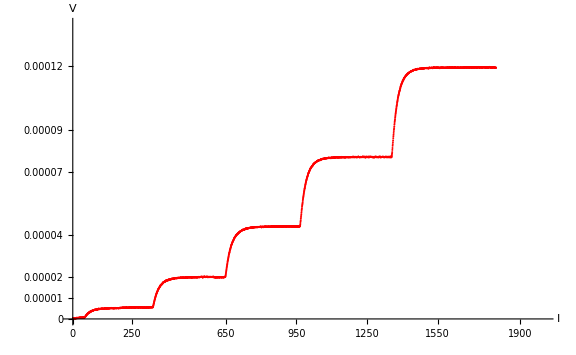

```mathematica
a=ListPlot[all,PlotMarkers->{Automatic, 2}, PlotStyle->{Red} , PlotRange->{{0,2000}, {0,0.00014}} ,
 AxesLabel->{" I", " V"}, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"" ,Ticks->{{0,100,250,500,650,800,950,1100,1250,1400,1550,1750,1900},{0,0.00001,0.00002,0.00004,0.00007,0.00009,0.00012}},AxesOrigin->{{0},{-0,00006}}]
```

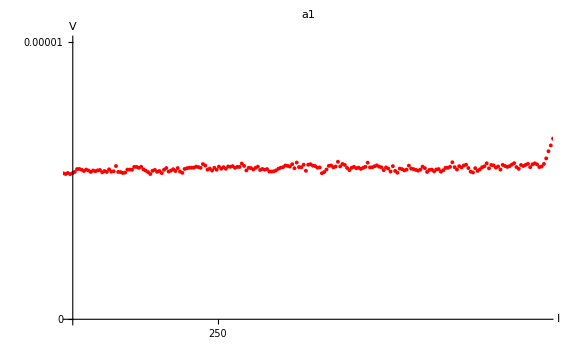

```mathematica
a1=ListPlot[all,PlotMarkers->{Automatic, 4}, PlotStyle->{Red} , PlotRange->{{210,340}, {0,0.00001}} ,
 AxesLabel->{" I", " V"}, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"a1" ,Ticks->{{0,100,250,500,650,800,950,1100,1250,1400,1550,1750,1900},{0,0.00001,0.00002,0.00004,0.00007,0.00009,0.00012}}]
```

```mathematica
a11=List[{210.545,5.30899854*^-6},{211.177,5.41100412*^-6},{211.809,5.41564073*^-6},{212.441,5.38780917*^-6},{213.073,5.34144304*^-6},{213.705,5.39244579*^-6},{214.337,5.35998949*^-6},{214.969,5.30894957*^-6},{215.601,5.35995218*^-6},{216.233,5.33676918*^-6},{216.865,5.36458879*^-6},{217.497,5.37849859*^-6},{218.129,5.29502461*^-6},{218.761,5.34139058*^-6},{219.394,5.3089344*^-6},{220.026,5.40166633*^-6},{220.658,5.31822524*^-6},{221.29,5.33213505*^-6},{221.922,5.52223575*^-6},{222.554,5.30895204*^-6},{223.186,5.30431544*^-6},{223.818,5.27189017*^-6},{224.451,5.28580001*^-6},{225.083,5.39244209*^-6},{225.715,5.39244209*^-6},{226.347,5.38781483*^-6},{226.979,5.48982036*^-6},{227.611,5.48982036*^-6},{228.243,5.45736406*^-6},{228.875,5.49445698*^-6},{229.507,5.40171713*^-6},{230.139,5.355351*^-6},{230.771,5.30434826*^-6},{231.403,5.23479906*^-6},{232.035,5.35069798*^-6},{232.667,5.38315424*^-6},{233.299,5.31360512*^-6},{233.931,5.34142477*^-6},{234.563,5.26723904*^-6},{235.195,5.38777265*^-6},{235.827,5.44804847*^-6},{236.459,5.32286022*^-6},{237.091,5.35531643*^-6},{237.723,5.40633551*^-6},{238.355,5.34142301*^-6},{238.987,5.44806498*^-6},{239.619,5.32287659*^-6},{240.251,5.27651051*^-6},{240.883,5.41560885*^-6},{241.515,5.44342849*^-6},{242.147,5.45733831*^-6},{242.779,5.46197492*^-6},{243.411,5.46198012*^-6},{244.043,5.49907299*^-6},{244.675,5.48516316*^-6},{245.307,5.45734351*^-6},{245.939,5.5918173*^-6},{246.571,5.54081457*^-6},{247.201,5.39244296*^-6},{247.833,5.42953586*^-6},{248.465,5.35998668*^-6},{249.097,5.45734217*^-6},{249.729,5.38779305*^-6},{250.361,5.49907165*^-6},{250.993,5.42488592*^-6},{251.625,5.48051101*^-6},{252.257,5.42487176*^-6},{252.889,5.50369403*^-6},{253.521,5.49442082*^-6},{254.153,5.51760384*^-6},{254.785,5.45732512*^-6},{255.417,5.48978134*^-6},{256.049,5.48978134*^-6},{256.681,5.61033302*^-6},{257.314,5.52687416*^-6},{257.945,5.36460816*^-6},{258.577,5.45734031*^-6},{259.209,5.4480671*^-6},{259.841,5.39706441*^-6},{260.473,5.45736299*^-6},{261.105,5.49909253*^-6},{261.737,5.37854054*^-6},{262.369,5.41563346*^-6},{263.001,5.38781377*^-6},{263.633,5.41098715*^-6},{264.265,5.32289153*^-6},{264.897,5.32289153*^-6},{265.529,5.33216475*^-6},{266.161,5.36461044*^-6},{266.793,5.42488635*^-6},{267.425,5.46197922*^-6},{268.057,5.48052565*^-6},{268.689,5.54080156*^-6},{269.321,5.52690203*^-6},{269.952,5.50371897*^-6},{270.584,5.58717798*^-6},{271.216,5.44344302*^-6},{271.848,5.64746413*^-6},{272.48,5.48518261*^-6},{273.112,5.47590938*^-6},{273.744,5.56864167*^-6},{274.376,5.35072078*^-6},{275.007,5.56861487*^-6},{275.639,5.5871613*^-6},{276.271,5.53615863*^-6},{276.903,5.52224881*^-6},{277.535,5.46198039*^-6},{278.167,5.47125361*^-6},{278.799,5.26260621*^-6},{279.431,5.30433569*^-6},{280.063,5.39706786*^-6},{280.695,5.52691288*^-6},{281.327,5.54082272*^-6},{281.959,5.47591011*^-6},{282.591,5.5037298*^-6},{283.223,5.67528316*^-6},{283.855,5.50836503*^-6},{284.487,5.59646071*^-6},{285.119,5.55936779*^-6},{285.751,5.45272565*^-6},{286.383,5.3739088*^-6},{287.015,5.4573679*^-6},{287.647,5.49446083*^-6},{288.279,5.44345805*^-6},{288.911,5.46199123*^-6},{289.543,5.42026172*^-6},{290.175,5.45735462*^-6},{290.807,5.49444752*^-6},{291.439,5.64281911*^-6},{292.071,5.47125062*^-6},{292.703,5.47588723*^-6},{293.335,5.51298009*^-6},{293.967,5.54543635*^-6},{294.599,5.49906975*^-6},{295.231,5.47588671*^-6},{295.863,5.37388134*^-6},{296.495,5.4712501*^-6},{297.127,5.42952063*^-6},{297.759,5.32288937*^-6},{298.391,5.51762703*^-6},{299.023,5.34607242*^-6},{299.655,5.28115987*^-6},{300.287,5.4295308*^-6},{300.919,5.41098436*^-6},{301.551,5.36461825*^-6},{302.183,5.39243791*^-6},{302.815,5.53617285*^-6},{303.447,5.42949562*^-6},{304.079,5.41094922*^-6},{304.711,5.38312962*^-6},{305.343,5.35531002*^-6},{305.975,5.3923945*^-6},{306.607,5.49903624*^-6},{307.239,5.44339707*^-6},{307.845,5.30893575*^-6},{308.503,5.38312131*^-6},{309.135,5.3924434*^-6},{309.767,5.33216744*^-6},{310.399,5.39708001*^-6},{311.031,5.41098985*^-6},{311.663,5.31827104*^-6},{312.295,5.36927383*^-6},{312.927,5.45736955*^-6},{313.559,5.45736955*^-6},{314.191,5.49446248*^-6},{314.823,5.65673535*^-6},{315.455,5.48054401*^-6},{316.087,5.39708495*^-6},{316.719,5.51763692*^-6},{317.351,5.4712694*^-6},{317.983,5.54081861*^-6},{318.615,5.56863829*^-6},{319.247,5.44808633*^-6},{319.879,5.31826114*^-6},{320.511,5.29044028*^-6},{321.143,5.44344853*^-6},{321.775,5.34607964*^-6},{322.407,5.40171901*^-6},{323.039,5.47588129*^-6},{323.671,5.51297414*^-6},{324.303,5.61961607*^-6},{324.935,5.43878844*^-6},{325.567,5.5593402*^-6},{326.199,5.54542577*^-6},{326.831,5.46660349*^-6},{327.463,5.50369633*^-6},{328.095,5.39241782*^-6},{328.727,5.56400659*^-6},{329.359,5.52227705*^-6},{329.991,5.48982074*^-6},{330.623,5.51764043*^-6},{331.255,5.57327982*^-6},{331.887,5.62427942*^-6},{332.519,5.48518099*^-6},{333.151,5.42026838*^-6},{333.783,5.55936682*^-6},{334.415,5.52226028*^-6},{335.047,5.56398977*^-6},{335.679,5.60108265*^-6},{336.311,5.48053078*^-6},{336.943,5.58253621*^-6},{337.575,5.61962659*^-6},{338.207,5.58253371*^-6},{338.839,5.48516492*^-6},{339.471,5.50371135*^-6},{340.103,5.59643559*^-6},{340.735,5.79580968*^-6}];
Mean[a11]
```

{275.64,5.44451×10^-6}

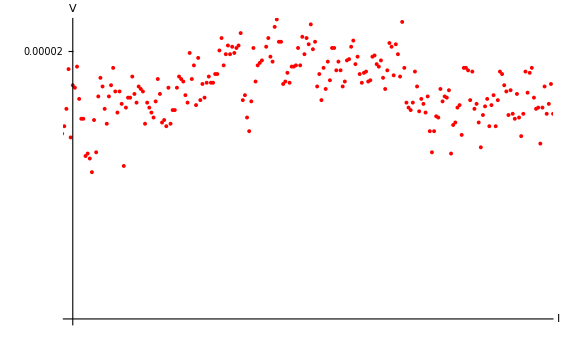

```mathematica
a2=ListPlot[all,PlotMarkers->{Automatic, 4}, PlotStyle->{Red} , PlotRange->{{500,640}, {0.000019,0.0000201}} ,
 AxesLabel->{" I", " V"}, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"" ,Ticks->{{0,100,250,500,650,800,950,1100,1250,1400,1550,1750,1900},{0,0.00001,0.00002,0.00004,0.00007,0.00009,0.00012}}]
```

```mathematica
a22=List[{500.001,0.0000198725382},{500.633,0.000019863265},{501.265,0.0000199421325},{501.897,0.0000198215806},{502.529,0.0000197473948},{503.135,0.0000197473948},{503.793,0.0000196082964},{504.425,0.0000196175384},{505.057,0.0000195989919},{505.689,0.0000195479893},{506.321,0.0000197427268},{506.953,0.0000196221553},{507.585,0.0000198308025},{508.218,0.0000199003516},{508.85,0.0000198678954},{509.482,0.0000197844365},{510.114,0.0000197288476},{510.746,0.0000198308531},{511.378,0.0000198725826},{512.01,0.0000199374952},{512.642,0.0000198494094},{513.274,0.000019770587},{513.906,0.0000198494094},{514.538,0.0000198030433},{515.17,0.0000195712126},{515.802,0.0000197890998},{516.434,0.0000198261927},{517.066,0.0000198261927},{517.698,0.0000199050151},{518.33,0.0000198400842},{518.962,0.0000198076279},{519.594,0.0000198679038},{520.226,0.0000198586306},{520.858,0.0000198493574},{521.49,0.0000197288169},{522.122,0.0000198076392},{522.754,0.0000197890928},{523.386,0.0000197705464},{524.018,0.0000197520189},{524.65,0.0000198122948},{525.282,0.0000198957538},{525.914,0.0000198401145},{526.546,0.0000197334725},{527.178,0.0000197427665},{527.81,0.0000197195834},{528.442,0.0000198633184},{529.074,0.0000197288566},{529.706,0.0000197798943},{530.338,0.0000197798943},{530.97,0.0000198633534},{531.602,0.000019905083},{532.234,0.0000198957846},{532.866,0.0000198865114},{533.498,0.0000198355086},{534.13,0.0000198076889},{534.762,0.0000199931535},{535.394,0.0000198958098},{536.026,0.0000199468126},{536.658,0.0000197984408},{537.29,0.0000199746324},{537.922,0.0000198170339},{538.554,0.0000198773101},{539.186,0.0000198263072},{539.818,0.0000198819467},{540.45,0.0000199051298},{541.082,0.0000198819649},{541.714,0.0000198819649},{542.346,0.0000199144213},{542.978,0.0000199144213},{543.61,0.0000200024559},{544.242,0.0000200488221},{544.874,0.0000199468165},{545.506,0.000019988546},{546.138,0.0000200210024},{546.77,0.0000199885012},{547.402,0.0000200163208},{548.034,0.0000199931378},{548.666,0.0000200116842},{549.298,0.0000200209701},{549.93,0.0000200673362},{550.562,0.000019816959},{551.194,0.0000198355055},{551.826,0.0000197520464},{552.458,0.0000197010499},{553.09,0.0000198123287},{553.722,0.0000200117031},{554.354,0.0000198865145},{554.986,0.0000199468426},{555.618,0.0000199561159},{556.25,0.0000199653891},{556.882,0.0000201415808},{557.514,0.000020016392},{558.146,0.0000200487969},{558.778,0.0000199792476},{559.41,0.0000199607012},{560.042,0.0000200905264},{560.673,0.0000201183258},{561.305,0.0000200348668},{561.937,0.0000200348668},{562.569,0.0000198772219},{563.201,0.0000198864952},{563.833,0.000019919011},{564.465,0.000019881918},{565.097,0.0000199421941},{565.729,0.0000199421941},{566.361,0.0000199468366},{566.993,0.0000200117493},{567.625,0.0000199468366},{568.257,0.0000200534789},{568.889,0.0000199885662},{569.521,0.0000200488499},{570.153,0.0000200256668},{570.785,0.0000200998527},{571.417,0.0000200071203},{572.049,0.0000200349144},{572.681,0.000019867996},{573.313,0.0000199143622},{573.945,0.0000198169932},{574.577,0.0000199375453},{575.209,0.0000198587206},{575.841,0.0000199607263},{576.473,0.000019891177},{577.105,0.0000200117291},{577.737,0.0000200117487},{578.369,0.0000199282895},{579.001,0.0000199607459},{579.633,0.0000199282895},{580.265,0.0000198680134},{580.897,0.000019886509},{581.529,0.0000199653315},{582.161,0.0000199699681},{582.793,0.0000200163342},{583.425,0.000020039496},{584.057,0.0000199514004},{584.689,0.0000199792201},{585.321,0.0000199143075},{585.953,0.0000198818129},{586.585,0.0000199189057},{587.217,0.0000199235423},{587.849,0.0000198864495},{588.481,0.0000198910861},{589.113,0.0000199791552},{589.745,0.0000199837918},{590.377,0.0000199513356},{591.009,0.0000199420624},{591.641,0.0000199652886},{592.273,0.0000199003761},{592.905,0.0000198586466},{593.537,0.0000199281958},{594.168,0.0000200302012},{594.8,0.0000200163005},{595.432,0.0000199096585},{596.064,0.0000200255737},{596.696,0.0000199884808},{597.328,0.0000199050369},{597.96,0.0000201090478},{598.592,0.0000199374932},{599.224,0.000019807668},{599.856,0.0000197891216},{600.488,0.0000197798729},{601.12,0.0000198076926},{601.752,0.000019923608},{602.384,0.0000198679686},{603.016,0.0000197752107},{603.648,0.0000198215768},{604.28,0.0000198030304},{604.912,0.0000197705741},{605.544,0.0000198308501},{606.176,0.0000197010072},{606.808,0.0000196221848},{607.44,0.0000197010072},{608.072,0.0000197566465},{608.704,0.0000197520117},{609.336,0.0000198586537},{609.968,0.0000198122876},{610.6,0.0000198308341},{611.232,0.0000198261975},{611.864,0.0000198540016},{612.496,0.0000196175346},{613.128,0.0000197241766},{613.76,0.0000197334498},{614.392,0.0000197891194},{615.024,0.0000197983926},{615.656,0.000019687114},{616.288,0.000019937491},{616.92,0.000019937491},{617.552,0.0000199282689},{618.184,0.0000198169901},{618.816,0.0000199236323},{619.448,0.0000197845337},{620.08,0.000019803096},{620.712,0.0000197335466},{621.344,0.0000196408142},{621.976,0.0000197613664},{622.608,0.0000197938227},{623.24,0.0000198216079},{623.872,0.0000197196023},{624.504,0.0000197984248},{625.136,0.0000198355177},{625.768,0.0000197195704},{626.4,0.0000198169392},{627.032,0.0000199235813},{627.665,0.000019914308},{628.297,0.0000198725785},{628.929,0.0000198494219},{629.561,0.0000197613262},{630.193,0.0000198540585},{630.825,0.0000197659628},{631.457,0.0000197474052},{632.089,0.0000198401375},{632.721,0.0000197520418},{633.353,0.0000196824926},{633.985,0.0000197659517},{634.617,0.0000199236055},{635.249,0.000019844783},{635.881,0.0000199189688},{636.513,0.0000199375153},{637.145,0.0000198262289},{637.777,0.0000197844994},{638.409,0.000019789136},{639.041,0.0000196546742},{639.673,0.0000197890942},{640.305,0.0000198679165}];
Mean[a22]
```

{570.153,0.0000198685}

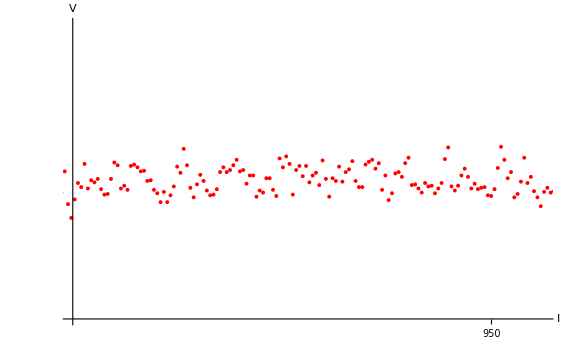

```mathematica
a3=ListPlot[all,PlotMarkers->{Automatic, 4}, PlotStyle->{Red} , PlotRange->{{870,960}, {0.000043,0.000045}} ,
 AxesLabel->{" I", " V"}, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"" ,Ticks->{{0,100,250,500,650,800,950,1100,1250,1400,1550,1750,1900},{0,0.00001,0.00002,0.00004,0.00007,0.00009,0.00012}},AxesOrigin->{{0},{-0,00006}}]
```

```mathematica
a33=List[{870.356,0.0000438114486},{870.988,0.0000439227274},{871.62,0.0000438949284},{872.252,0.0000440525734},{872.884,0.0000438856552},{873.516,0.0000439412946},{874.148,0.0000439273847},{874.781,0.0000439505445},{875.413,0.0000438809953},{876.045,0.0000438439024},{876.677,0.000043848539},{877.309,0.0000439505712},{877.941,0.00004406185},{878.573,0.0000440433035},{879.205,0.0000438856585},{879.837,0.000043904205},{880.469,0.000043876387},{881.101,0.0000440386687},{881.733,0.0000440479419},{882.365,0.0000440293954},{882.997,0.0000440015406},{883.629,0.0000440061772},{884.261,0.000043936628},{884.893,0.0000439412646},{885.525,0.000043876352},{886.157,0.0000438532219},{886.789,0.0000437929458},{887.421,0.0000438624951},{888.053,0.0000437929458},{888.685,0.0000438393805},{889.317,0.0000438996566},{889.949,0.0000440341187},{890.581,0.0000439923891},{891.213,0.000044154671},{891.845,0.0000440433548},{892.477,0.0000438903463},{893.109,0.0000438254336},{893.741,0.0000439135294},{894.373,0.0000439784013},{895.005,0.0000439366718},{895.637,0.0000438717591},{896.269,0.0000438393028},{896.901,0.0000438439394},{897.533,0.0000438810484},{898.165,0.0000439969639},{898.797,0.0000440294203},{899.429,0.0000439969639},{900.061,0.0000440109635},{900.693,0.0000440434199},{901.325,0.0000440805129},{901.957,0.0000440016902},{902.589,0.0000440109635},{903.221,0.0000439182482},{903.853,0.0000439738877},{904.485,0.0000439738877},{905.117,0.0000438301522},{905.749,0.0000438717603},{906.381,0.0000438578505},{907.013,0.0000439552195},{907.645,0.0000439552195},{908.277,0.0000438763969},{908.909,0.0000438346036},{909.541,0.0000440896174},{910.173,0.0000440293414},{910.805,0.0000441035272},{911.437,0.0000440524711},{912.069,0.0000438438238},{912.701,0.0000440107417},{913.333,0.0000440385613},{913.965,0.0000439690532},{914.597,0.0000440386024},{915.229,0.0000439273237},{915.861,0.0000439736898},{916.493,0.0000439922362},{917.125,0.0000439088202},{917.757,0.0000440757384},{918.389,0.0000439505497},{919.02,0.0000438299977},{919.652,0.0000439551732},{920.284,0.0000439366268},{920.916,0.0000440339957},{921.548,0.0000439319901},{922.18,0.0000439969027},{922.812,0.0000440155697},{923.444,0.0000440712092},{924.076,0.0000439367471},{924.708,0.0000438950174},{925.34,0.0000438949744},{925.972,0.000044047983},{926.604,0.0000440665294},{927.236,0.0000440804393},{927.868,0.0000440201632},{928.5,0.0000440572942},{929.132,0.0000438764658},{929.764,0.0000439738349},{930.396,0.0000438069164},{931.028,0.0000438533533},{931.66,0.0000439878156},{932.292,0.0000439970888},{932.924,0.0000439646324},{933.556,0.000044057365},{934.188,0.000044094284},{934.82,0.0000439088194},{935.452,0.000043913456},{936.084,0.0000438856363},{936.716,0.0000438578172},{937.348,0.0000439227298},{937.98,0.0000438995467},{938.612,0.0000439041833},{939.244,0.0000438531806},{939.876,0.0000438857676},{940.506,0.0000439228607},{941.138,0.0000440851426},{941.77,0.0000441639653},{942.402,0.0000438997026},{943.034,0.0000438718829},{943.666,0.0000439043393},{944.298,0.0000439738887},{944.93,0.000044020255},{945.562,0.0000439644963},{946.194,0.0000438856737},{946.826,0.0000439181301},{947.458,0.0000438810371},{948.09,0.0000438902817},{948.722,0.0000438949184},{949.354,0.000043839279},{949.986,0.0000438346423},{950.618,0.0000438810085},{951.25,0.0000440248247},{951.882,0.0000441685601},{952.514,0.0000440804642},{953.146,0.0000439552754},{953.778,0.0000439969286},{954.41,0.0000438253738},{955.042,0.0000438485568},{955.674,0.0000439320159},{956.306,0.0000440942975},{956.938,0.0000439227578},{957.57,0.0000439644873},{958.176,0.0000438671183},{958.834,0.0000438253888},{959.466,0.0000437652036},{960.098,0.0000438625728}];
Mean[a33]
```

{915.228,0.0000439469}

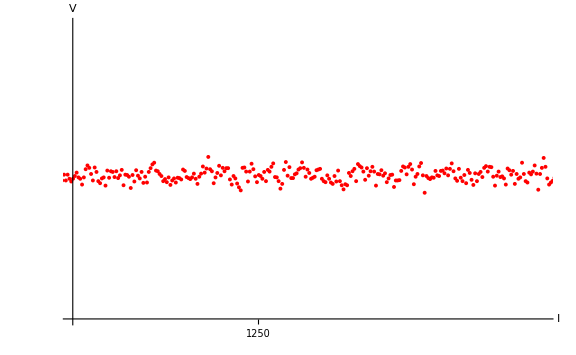

```mathematica
a4=ListPlot[all,PlotMarkers->{Automatic, 4}, PlotStyle->{Red} , PlotRange->{{1185,1350}, {0.000075,0.000079}} ,
 AxesLabel->{" I", " V"}, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"" ,Ticks->{{0,100,250,500,650,800,950,1100,1250,1400,1550,1750,1900},{0,0.00001,0.00002,0.00004,0.00007,0.00009,0.00012}},AxesOrigin->{{0},{-0,00006}}]
```

```mathematica
a44=List[{1180.037,0.0000768615127},{1180.669,0.0000769264256},{1181.301,0.0000768800593},{1181.933,0.000076958894},{1182.565,0.0000768800713},{1183.197,0.000076958894},{1183.829,0.0000769032545},{1184.461,0.0000768661736},{1185.093,0.0000769032666},{1185.725,0.0000769403597},{1186.357,0.000076986726},{1186.989,0.0000769218131},{1187.621,0.0000769031993},{1188.253,0.0000768243767},{1188.885,0.0000769217458},{1189.517,0.0000770330249},{1190.149,0.0000770840574},{1190.781,0.000077051601},{1191.413,0.0000769681416},{1192.045,0.0000768800457},{1192.677,0.0000770562376},{1193.309,0.0000769958554},{1193.941,0.0000768706665},{1194.573,0.0000768428468},{1195.205,0.0000769077595},{1195.837,0.0000769216568},{1196.469,0.0000768103779},{1197.102,0.0000770143893},{1197.734,0.0000769170202},{1198.366,0.000077005116},{1198.998,0.0000769959388},{1199.63,0.0000769263894},{1200.262,0.000077005212},{1200.894,0.0000769124795},{1201.526,0.0000769496115},{1202.158,0.0000770237976},{1202.79,0.0000768151492},{1203.422,0.0000769588848},{1204.054,0.0000769542481},{1204.687,0.0000769310231},{1205.318,0.0000767780144},{1205.95,0.0000769542062},{1206.582,0.0000768661103},{1207.214,0.0000770191421},{1207.846,0.000076944956},{1208.478,0.000076907863},{1209.11,0.0000769959589},{1209.742,0.0000768475868},{1210.374,0.0000769311436},{1211.006,0.0000768523208},{1211.638,0.0000769960565},{1212.27,0.0000770470595},{1212.902,0.0000770979283},{1213.534,0.0000771211114},{1214.166,0.000077014469},{1214.798,0.0000770051957},{1215.43,0.0000769681027},{1216.062,0.0000769402405},{1216.694,0.0000768706911},{1217.326,0.0000768985109},{1217.958,0.0000768567813},{1218.59,0.000076921694},{1219.222,0.0000768196593},{1219.854,0.0000768799354},{1220.486,0.0000769077552},{1221.118,0.0000768521157},{1221.75,0.0000769170945},{1222.356,0.0000769124579},{1223.014,0.0000768939114},{1223.647,0.0000770283736},{1224.279,0.0000770098271},{1224.911,0.0000769265092},{1225.543,0.0000769125993},{1226.175,0.0000768986894},{1226.807,0.0000769218726},{1227.439,0.0000769727255},{1228.071,0.0000769031761},{1228.703,0.0000768336267},{1229.335,0.0000769309959},{1229.967,0.0000769727255},{1230.599,0.0000770698928},{1231.231,0.0000769864337},{1231.863,0.0000770420731},{1232.495,0.000077199718},{1233.127,0.0000770327951},{1233.759,0.0000770049754},{1234.391,0.0000768426939},{1235.023,0.0000769215164},{1235.655,0.0000769817924},{1236.287,0.0000770793548},{1236.919,0.0000769495292},{1237.551,0.000077051535},{1238.183,0.0000770051688},{1238.815,0.0000770470103},{1239.447,0.0000770470103},{1240.079,0.0000768940015},{1240.711,0.000076824452},{1241.343,0.0000769403678},{1241.975,0.0000769079018},{1242.607,0.0000768383523},{1243.239,0.0000767873494},{1243.871,0.0000767456197},{1244.503,0.0000770516852},{1245.135,0.0000770563218},{1245.767,0.0000770006822},{1246.399,0.0000768662198},{1247.031,0.0000770006822},{1247.663,0.000077107335},{1248.295,0.0000770331488},{1248.927,0.0000769357795},{1249.559,0.0000768569567},{1250.191,0.000076954199},{1250.823,0.0000769402891},{1251.455,0.0000769031961},{1252.087,0.0000769959287},{1252.719,0.0000768707397},{1253.351,0.0000770237494},{1253.983,0.0000770005663},{1254.615,0.000077065479},{1255.247,0.0000771118453},{1255.879,0.0000769264421},{1256.511,0.0000769218054},{1257.143,0.0000768708025},{1257.775,0.0000767687966},{1258.407,0.0000768337094},{1259.039,0.0000770237656},{1259.671,0.0000771304081},{1260.303,0.0000769449429},{1260.935,0.0000770608587},{1261.567,0.000076912479},{1262.199,0.000076912479},{1262.831,0.0000769634819},{1263.463,0.0000769773918},{1264.095,0.0000770283947},{1264.727,0.0000770468779},{1265.359,0.0000771257005},{1265.991,0.0000770515145},{1266.623,0.0000769309623},{1267.255,0.0000770282901},{1267.887,0.0000769819239},{1268.519,0.0000769031013},{1269.151,0.0000769170112},{1269.783,0.000076930921},{1270.415,0.0000770190781},{1271.047,0.0000770283513},{1271.679,0.0000770376246},{1272.311,0.0000769031624},{1272.943,0.0000768706949},{1273.575,0.000076856785},{1274.207,0.0000769495175},{1274.839,0.0000769031513},{1275.471,0.0000768521484},{1276.103,0.0000768336153},{1276.735,0.0000769402577},{1277.367,0.0000768660717},{1277.999,0.0000770144438},{1278.631,0.0000768707146},{1279.263,0.000076815075},{1279.895,0.0000767594355},{1280.527,0.0000768289849},{1281.159,0.000076815075},{1281.791,0.0000769821438},{1282.423,0.0000769404141},{1283.055,0.0000770053269},{1283.687,0.0000770377834},{1284.319,0.0000768708147},{1284.951,0.0000771026463},{1285.583,0.0000770748265},{1286.215,0.00007705628},{1286.847,0.0000770006404},{1287.477,0.0000768891571},{1288.109,0.0000770468022},{1288.741,0.0000769447965},{1289.373,0.0000770050726},{1290.005,0.0000770654416},{1290.637,0.0000770005289},{1291.269,0.0000768104272},{1291.901,0.0000769680725},{1292.533,0.0000769634359},{1293.165,0.000077019188},{1293.797,0.0000769450019},{1294.429,0.0000769774584},{1295.061,0.0000768569059},{1295.693,0.0000769078952},{1296.325,0.0000769542615},{1296.957,0.0000769588981},{1297.589,0.0000767919794},{1298.221,0.0000768800754},{1298.853,0.0000768800168},{1299.485,0.0000768846535},{1300.117,0.0000770098424},{1300.749,0.0000770701186},{1301.381,0.0000770561611},{1302.013,0.0000769634286},{1302.645,0.0000770654343},{1303.277,0.0000771025273},{1303.909,0.0000770283413},{1304.541,0.0000768290854},{1305.173,0.0000769310913},{1305.805,0.0000769681843},{1306.437,0.0000770701902},{1307.069,0.0000771166457},{1307.701,0.0000769497268},{1308.334,0.0000767132583},{1308.966,0.0000769404535},{1309.598,0.0000769126337},{1310.23,0.0000768986858},{1310.862,0.0000769218689},{1311.494,0.0000769172323},{1312.126,0.000077009965},{1312.758,0.0000769496887},{1313.39,0.0000769404345},{1314.022,0.000077009984},{1314.654,0.0000770146207},{1315.286,0.0000769775276},{1315.918,0.000077042459},{1316.551,0.0000769497263},{1317.183,0.0000770378224},{1317.815,0.0000771120086},{1318.447,0.000077005366},{1319.079,0.0000769080192},{1319.711,0.0000768755627},{1320.343,0.000077037845},{1320.975,0.0000769172924},{1321.607,0.0000768707333},{1322.239,0.0000769541926},{1322.871,0.0000768429136},{1323.503,0.000077023742},{1324.135,0.0000769820124},{1324.767,0.0000768891327},{1325.399,0.0000768195834},{1326.031,0.0000769772285},{1326.663,0.0000768705862},{1327.295,0.0000769680774},{1327.927,0.0000769958972},{1328.559,0.0000769263478},{1329.191,0.0000770515367},{1329.823,0.0000770747198},{1330.455,0.000077000651},{1331.087,0.0000770655639},{1331.719,0.0000770609272},{1332.351,0.0000769311015},{1332.983,0.0000768104485},{1333.615,0.0000769449107},{1334.247,0.0000770005502},{1334.879,0.0000769263642},{1335.511,0.0000769356374},{1336.143,0.0000769078247},{1336.775,0.0000768243654},{1337.407,0.0000770422869},{1338.039,0.0000770191038},{1338.671,0.0000769589663},{1339.303,0.0000770099693},{1339.935,0.0000768337772},{1340.567,0.0000769682396},{1341.199,0.0000769033267},{1341.831,0.0000769218033},{1342.463,0.0000771211784},{1343.095,0.0000769681696},{1343.727,0.0000768708004},{1344.359,0.0000768521211},{1344.991,0.0000769865832},{1345.623,0.0000769634},{1346.255,0.000077000493},{1346.887,0.0000770839523},{1347.519,0.0000769726613},{1348.151,0.00007675474},{1348.783,0.0000769680246},{1349.415,0.0000770514839}];
Mean[a44]
```

{1264.73,0.0000769521}

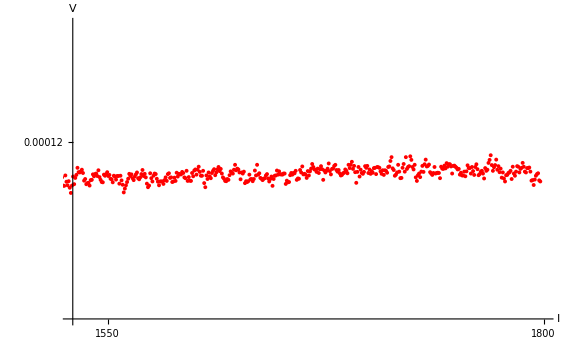

```mathematica
a5=ListPlot[all,PlotMarkers->{Automatic, 4}, PlotStyle->{Red} , PlotRange->{{1530,1800}, {0.000117,0.000122}} ,
 AxesLabel->{" I", " V"}, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"" ,Ticks->{{0,100,250,500,650,800,950,1100,1250,1400,1550,1750,1800},{0,0.00001,0.00002,0.00004,0.00007,0.00009,0.00012}},AxesOrigin->{{0},{-0,00006}}]
```

```mathematica
a55=List[{1530.167,0.000119416792},{1530.799,0.000119286966},{1531.431,0.000119393506},{1532.063,0.000119444509},{1532.695,0.000119565062},{1533.327,0.000119490876},{1533.959,0.000119486177},{1534.591,0.000119504724},{1535.223,0.000119532544},{1535.855,0.000119476904},{1536.487,0.000119347078},{1537.119,0.000119374867},{1537.751,0.000119286771},{1538.383,0.000119305317},{1539.015,0.000119309954},{1539.647,0.00011926351},{1540.279,0.000119356243},{1540.911,0.000119360879},{1541.543,0.000119453612},{1542.175,0.000119421155},{1542.807,0.000119458323},{1543.439,0.000119467596},{1544.071,0.000119425866},{1544.703,0.000119523235},{1545.335,0.000119407131},{1545.967,0.000119360764},{1546.599,0.000119323671},{1547.231,0.000119319035},{1547.863,0.00011944886},{1548.495,0.000119430179},{1549.127,0.000119457998},{1549.759,0.000119490455},{1550.391,0.000119425542},{1551.023,0.000119444201},{1551.655,0.000119379288},{1552.287,0.000119370015},{1552.919,0.000119319012},{1553.551,0.000119430291},{1554.183,0.000119416491},{1554.815,0.000119365488},{1555.447,0.000119425764},{1556.079,0.000119425764},{1556.711,0.000119295936},{1557.343,0.000119430398},{1557.975,0.000119351576},{1558.607,0.00011927739},{1559.239,0.000119147564},{1559.871,0.000119212256},{1560.503,0.000119267895},{1561.135,0.000119323535},{1561.767,0.000119379174},{1562.399,0.000119462649},{1563.031,0.000119425556},{1563.663,0.000119453375},{1564.295,0.000119388463},{1564.927,0.000119356006},{1565.559,0.000119416509},{1566.191,0.000119453602},{1566.823,0.000119486059},{1567.455,0.000119388689},{1568.087,0.000119370396},{1568.719,0.000119402852},{1569.351,0.000119458492},{1569.983,0.000119528042},{1570.615,0.000119426036},{1571.247,0.00011946296},{1571.879,0.000119402683},{1572.511,0.000119296041},{1573.143,0.000119235765},{1573.775,0.000119263534},{1574.407,0.000119472182},{1575.039,0.000119388723},{1575.671,0.000119333083},{1576.303,0.000119430453},{1576.935,0.000119467711},{1577.567,0.000119458438},{1578.199,0.000119379615},{1578.831,0.000119328612},{1579.463,0.00011926839},{1580.095,0.000119333303},{1580.727,0.000119333303},{1581.359,0.000119333303},{1581.991,0.000119291573},{1582.623,0.000119356411},{1583.255,0.000119402778},{1583.887,0.000119342501},{1584.519,0.000119458417},{1585.151,0.000119472165},{1585.783,0.000119393343},{1586.415,0.000119402616},{1587.047,0.000119323793},{1587.679,0.000119333105},{1588.311,0.000119398018},{1588.943,0.000119342378},{1589.575,0.000119481477},{1590.207,0.000119416564},{1590.839,0.000119462863},{1591.471,0.00011945359},{1592.103,0.00011945359},{1592.735,0.000119495319},{1593.367,0.000119476925},{1593.999,0.000119402738},{1594.631,0.000119388829},{1595.263,0.000119514018},{1595.895,0.000119342462},{1596.527,0.000119407468},{1597.159,0.000119347192},{1597.791,0.000119342556},{1598.423,0.000119477018},{1599.055,0.000119421178},{1599.687,0.000119518547},{1600.32,0.000119537093},{1600.952,0.000119448997},{1601.584,0.000119532457},{1602.216,0.000119583634},{1602.848,0.000119495538},{1603.48,0.000119430625},{1604.112,0.000119430625},{1604.744,0.00011951409},{1605.376,0.000119305441},{1606.008,0.000119235892},{1606.64,0.000119435267},{1607.272,0.000119374991},{1607.904,0.000119485857},{1608.536,0.000119420944},{1609.168,0.000119388488},{1609.8,0.000119476584},{1610.432,0.000119513797},{1611.064,0.000119541617},{1611.696,0.000119439611},{1612.328,0.000119485977},{1612.96,0.00011953698},{1613.592,0.000119579035},{1614.225,0.000119509485},{1614.857,0.000119546578},{1615.489,0.000119467756},{1616.121,0.000119402704},{1616.753,0.000119379521},{1617.385,0.000119342428},{1618.017,0.000119337791},{1618.649,0.000119374884},{1619.281,0.000119360752},{1619.913,0.000119439574},{1620.545,0.000119504487},{1621.177,0.000119481304},{1621.809,0.00011946737},{1622.441,0.000119532282},{1623.073,0.000119615742},{1623.705,0.000119523009},{1624.337,0.000119550829},{1624.969,0.000119536855},{1625.601,0.000119485852},{1626.233,0.000119369936},{1626.865,0.000119485852},{1627.497,0.000119467201},{1628.129,0.000119499657},{1628.761,0.000119304919},{1629.393,0.000119337376},{1630.025,0.000119323466},{1630.657,0.000119337551},{1631.289,0.00011944883},{1631.921,0.000119370007},{1632.553,0.000119374644},{1633.185,0.000119337789},{1633.815,0.000119374882},{1634.447,0.000119518618},{1635.079,0.000119435159},{1635.711,0.000119615987},{1636.343,0.000119449},{1636.975,0.000119472183},{1637.607,0.00011939336},{1638.24,0.00011937945},{1638.872,0.000119356223},{1639.504,0.000119379406},{1640.136,0.000119388679},{1640.768,0.000119435046},{1641.4,0.000119458229},{1642.032,0.000119384257},{1642.664,0.000119333254},{1643.296,0.000119374984},{1643.928,0.000119416714},{1644.56,0.000119259082},{1645.192,0.000119374998},{1645.824,0.000119430637},{1646.456,0.000119435274},{1647.088,0.000119518722},{1647.72,0.000119449172},{1648.352,0.000119504812},{1648.984,0.000119453809},{1649.616,0.000119453809},{1650.248,0.000119449155},{1650.88,0.000119467701},{1651.512,0.000119467701},{1652.144,0.000119291509},{1652.776,0.000119347071},{1653.408,0.000119319252},{1654.04,0.000119323888},{1654.672,0.000119439804},{1655.304,0.000119476897},{1655.936,0.000119449017},{1656.568,0.000119476837},{1657.2,0.0001194722},{1657.832,0.00011951393},{1658.464,0.000119360873},{1659.096,0.000119384056},{1659.728,0.000119379419},{1660.36,0.000119527791},{1660.992,0.000119486062},{1661.624,0.000119588085},{1662.256,0.000119453623},{1662.888,0.000119462896},{1663.52,0.000119448986},{1664.152,0.00011939337},{1664.784,0.000119509286},{1665.416,0.0001194351},{1666.048,0.000119504649},{1666.68,0.000119551015},{1667.312,0.000119629863},{1667.944,0.00011957886},{1668.576,0.000119537131},{1669.208,0.000119532494},{1669.84,0.000119495475},{1670.472,0.000119551115},{1671.104,0.000119476928},{1671.736,0.000119541841},{1672.368,0.000119592844},{1673.,0.000119541793},{1673.632,0.000119360964},{1674.264,0.00011951861},{1674.896,0.000119486154},{1675.528,0.000119513601},{1676.16,0.000119550694},{1676.792,0.000119638789},{1677.424,0.000119508964},{1678.056,0.000119453325},{1678.688,0.000119545958},{1679.32,0.000119555231},{1679.952,0.00011959696},{1680.584,0.000119615507},{1681.216,0.000119527488},{1681.848,0.000119499668},{1682.48,0.000119527488},{1683.112,0.000119471849},{1683.744,0.000119434756},{1684.376,0.000119444133},{1685.008,0.000119471953},{1685.64,0.000119481226},{1686.272,0.000119536866},{1686.904,0.000119513897},{1687.536,0.000119472167},{1688.168,0.000119615903},{1688.8,0.000119560263},{1689.432,0.000119615903},{1690.064,0.000119667099},{1690.696,0.000119546547},{1691.328,0.00011959755},{1691.96,0.000119490907},{1692.592,0.000119310205},{1693.224,0.000119495671},{1693.856,0.00011957913},{1694.488,0.000119416848},{1695.12,0.000119532764},{1695.752,0.000119477055},{1696.384,0.000119463145},{1697.016,0.000119495602},{1697.648,0.000119592971},{1698.28,0.00011956499},{1698.912,0.000119597447},{1699.544,0.000119476894},{1700.176,0.00011953717},{1700.808,0.000119462984},{1701.44,0.00011950914},{1702.072,0.00011948132},{1702.704,0.000119560143},{1703.336,0.000119564779},{1703.968,0.000119458241},{1704.6,0.000119578793},{1705.232,0.000119574157},{1705.864,0.000119564883},{1706.496,0.000119504773},{1707.128,0.000119463043},{1707.76,0.000119523319},{1708.392,0.000119444496},{1709.024,0.000119523319},{1709.656,0.000119513894},{1710.288,0.000119481438},{1710.92,0.000119578807},{1711.552,0.00011958808},{1712.184,0.000119680797},{1712.816,0.00011974571},{1713.448,0.000119555608},{1714.08,0.000119527789},{1714.712,0.000119430419},{1715.344,0.000119449088},{1715.976,0.000119486181},{1716.608,0.000119616007},{1717.24,0.000119500091},{1717.873,0.000119388829},{1718.505,0.000119393466},{1719.137,0.000119565021},{1719.769,0.000119629934},{1720.401,0.000119500108},{1721.033,0.000119745852},{1721.665,0.000119546476},{1722.297,0.000119578933},{1722.929,0.000119592843},{1723.561,0.000119759924},{1724.193,0.000119699647},{1724.825,0.000119579095},{1725.457,0.000119537365},{1726.089,0.000119616188},{1726.721,0.000119402736},{1727.353,0.00011934246},{1727.985,0.000119439829},{1728.617,0.000119467649},{1729.249,0.000119407174},{1729.881,0.000119499907},{1730.514,0.000119597276},{1731.146,0.00011949527},{1731.778,0.000119625096},{1732.41,0.000119703924},{1733.042,0.000119588009},{1733.674,0.000119597282},{1734.306,0.000119620465},{1734.938,0.00011949081},{1735.57,0.000119467627},{1736.202,0.000119444444},{1736.834,0.0001194769},{1737.466,0.000119578906},{1738.098,0.00011946783},{1738.73,0.000119477103},{1739.362,0.00011948174},{1739.994,0.000119477103},{1740.626,0.000119388862},{1741.258,0.000119583601},{1741.89,0.000119551144},{1742.522,0.000119546508},{1743.154,0.000119602147},{1743.786,0.000119555723},{1744.419,0.000119643819},{1745.051,0.000119583543},{1745.683,0.000119625273},{1746.315,0.000119625343},{1746.947,0.00011958825},{1747.579,0.000119467698},{1748.211,0.000119597523},{1748.843,0.00011960216},{1749.473,0.000119583694},{1750.105,0.000119565147},{1750.737,0.000119537327},{1751.369,0.000119546601},{1752.001,0.000119449216},{1752.633,0.000119481672},{1753.265,0.000119435306},{1753.897,0.000119435306},{1754.529,0.000119500219},{1755.161,0.000119421438},{1755.793,0.000119504898},{1756.425,0.000119606904},{1757.057,0.000119560537},{1757.689,0.000119560168},{1758.321,0.000119467435},{1758.953,0.000119578714},{1759.585,0.000119509165},{1760.217,0.000119444085},{1760.849,0.000119578547},{1761.479,0.000119624913},{1762.111,0.000119541454},{1762.743,0.000119439448},{1763.375,0.00011945819},{1764.007,0.00011949992},{1764.639,0.000119513829},{1765.271,0.000119467463},{1765.903,0.000119383887},{1766.535,0.000119560079},{1767.167,0.000119513713},{1767.799,0.000119532259},{1768.431,0.000119648175},{1769.063,0.000119699272},{1769.695,0.000119778095},{1770.327,0.000119611176},{1770.959,0.000119513807},{1771.591,0.000119574058},{1772.223,0.000119611151},{1772.855,0.000119703883},{1773.487,0.000119532328},{1774.119,0.000119592604},{1774.751,0.000119490704},{1775.383,0.00011955098},{1776.015,0.000119397972},{1776.647,0.000119486068},{1777.279,0.000119384248},{1777.911,0.000119333245},{1778.543,0.000119439887},{1779.176,0.000119444524},{1779.808,0.00011947698},{1780.44,0.000119485993},{1781.072,0.000119513813},{1781.704,0.000119374714},{1782.336,0.000119583363},{1782.968,0.000119467531},{1783.6,0.000119430438},{1784.232,0.000119499988},{1784.864,0.00011959272},{1785.496,0.000119583447},{1786.128,0.000119486253},{1786.76,0.000119546529},{1787.392,0.000119565076},{1788.024,0.000119648535},{1788.656,0.00011958353},{1789.288,0.000119500071},{1789.92,0.000119486161},{1790.552,0.000119560347},{1791.184,0.000119560347},{1791.816,0.000119569705},{1792.448,0.000119500156},{1793.08,0.000119347147},{1793.712,0.00011935642},{1794.344,0.000119273001},{1794.976,0.000119365734},{1795.608,0.000119430647},{1796.24,0.000119458467},{1796.872,0.000119472376},{1797.504,0.00011935177},{1798.136,0.000119333224}];
Mean[a55]
```

{1664.15,0.00011947}

```mathematica
tot=List[{10,5.444511200386476*^-6}, {20,0.00001986845818565023}, {30,0.00004394689934405594}, {40,0.00007695207582453534},{50,0.00011946985235294117}];
```

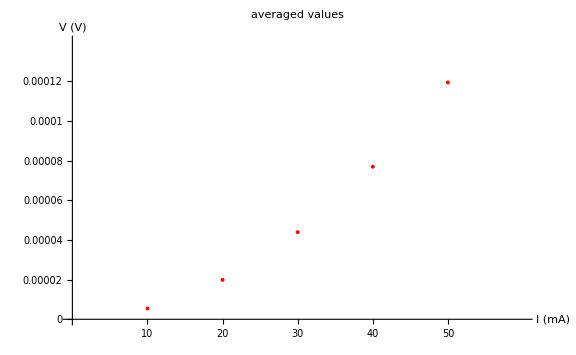

```mathematica
ptot=ListPlot[tot,PlotMarkers->{Automatic, 4}, PlotStyle->{Red} , PlotRange->{{0,60}, {0,0.00014}} ,
 AxesLabel->{" I (mA)", " V (V)"}, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"averaged values" ,Ticks->{{10,20,30,40,50},{0,0.00001,0.00002,0.00003,0.00004,0.00005,0.00006,0.00007,0.00008,0.00009,0.0001,0.00011,0.00012,0.00013}},AxesOrigin->{{0},{-0,00006}}]
```

```mathematica
Calculating k
```

```mathematica
Needs["ErrorBarPlots`"]

erp=ErrorListPlot[{{{10^2,5.444511200386476*^-6},ErrorBar[0,0.000001]}  ,{ {20^2,0.00001986845818565023},ErrorBar[0,0.000001]}  ,{ {30^2,0.00004394689934405594},ErrorBar[0,0.000001]}  ,{ {40^2,0.00007695207582453534},ErrorBar[0,0.000001]}  ,{{50^2,0.00011946985235294117},ErrorBar[0,0.000001]} },  PlotRange->{{0,3600}, {0,0.00013}} ,  AxesLabel->{" I^2 (mA)", " V (V)"}, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->" average V values" ,  Ticks->{{100,500,1000,2000,3000},{0,0.00001,0.00002,0.00003,0.00004,0.00005,0.00006,0.00007,0.00008,0.00009,0.0001,0.00011,0.00012,0.00013}}, PlotStyle->Directive[Thin,PointSize[Medium],Red,"LineColor"->Green], LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]],Method->
{"CoordinatesToolOptions"->{"DisplayFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}}]
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

-Graphics-

```mathematica
kapas=List[{10^2,5.444511200386476*^-6}  ,{20^2,0.00001986845818565023}  ,{30^2,0.00004394689934405594}, {40^2,0.00007695207582453534},{50^2,0.00011946985235294117}]


fit=LinearModelFit[kapas,{x},x]
```

{{100,5.44451×10^-6},{400,0.0000198685},{900,0.0000439469},{1600,0.0000769521},{2500,0.00011947}}

LinearModelFit::ivar: {4.74845×10^-8} is not a valid variable.

LinearModelFit[{{100,5.44451×10^-6},{400,0.0000198685},{900,0.0000439469},{1600,0.0000769521},{2500,0.00011947}},{4.74845×10^-8},4.74845×10^-8]

```mathematica
fit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 9.03412×10^-7 | 1.69537×10^-7 | 5.32871 | 0.0129155
x | 4.74845×10^-8 | 1.2116×10^-10 | 391.917 | 3.66335×10^-8

```mathematica
fit["AdjustedRSquared"]
```

0.999974

```mathematica
final=Show[erp,Plot[{ 9.034124970336821*^-7+4.748449716770923*^-8 x},{x,90,2600} , PlotStyle->{Blue, Dashed} ]]
```

-Graphics-

```mathematica
Calculate k
```

```mathematica
r=10;
l=49.8;
dl=0.5;
d=0.1111;
dd=0.0015;
b=15.28;
db=0.09;
A=d*b;
s=5.9*10^-5;
x=4.748449716770923*^-8;
dx=1.211595873809069*^-10;
dk= Sqrt[   (s*r*dl/(A*x) )^2     +   (s*l*r*dd/(A*d*x))^2   + (s*r*l*db/(A*b*x))^2   +  (s*r*l*dx/(A*b*x^2))^2      ]
```

6497.96

```mathematica
Solve[ x==r*s*l/(A*k),k]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{k→364495.}}

```mathematica
k10=s*l*r/(A*x10)
k20=s*l*r/(A*x20)
k30=s*l*r/(A*x30)
k40=s*l*r/(A*x40)
k50=s*l*r/(A*x50)
```

317896.

348449.

354453.

359868.

362181.

```mathematica
x10=5.444511200386476*^-6/100;
x20=0.00001986845818565023/400;
x30=0.00004394689934405594/900;
x40=0.00007695207582453534/1600;
x50=0.00011946985235294117/2500;
```

```mathematica
dk10= Sqrt[   (s*r*dl/(A*x10) )^2     +   (s*l*r*dd/(A*d*x10))^2   + (s*r*l*db/(A*b*x10))^2       ]
dk20= Sqrt[   (s*r*dl/(A*x20) )^2     +   (s*l*r*dd/(A*d*x20))^2   + (s*r*l*db/(A*b*x20))^2       ]
dk30= Sqrt[   (s*r*dl/(A*x30) )^2     +   (s*l*r*dd/(A*d*x30))^2   + (s*r*l*db/(A*b*x30))^2       ]
dk40= Sqrt[   (s*r*dl/(A*x40) )^2     +   (s*l*r*dd/(A*d*x40))^2   + (s*r*l*db/(A*b*x40))^2       ]
dk50= Sqrt[   (s*r*dl/(A*x50) )^2     +   (s*l*r*dd/(A*d*x50))^2   + (s*r*l*db/(A*b*x50))^2       ]
```

5666.97

6211.63

6318.65

6415.19

6456.42

```mathematica
ka=List[{10,317895.98705379124}, {20,348449.4359652573}, {30,354452.63695850276}, {40,359868.2933037525},{50,362180.96615687135}]
```

{{10,317896.},{20,348449.},{30,354453.},{40,359868.},{50,362181.}}

```mathematica
Needs["ErrorBarPlots`"]

kappplot=ErrorListPlot[{{{10,317895.98705379124},ErrorBar[0,5666.971883266383]}  ,{ {20,348449.4359652573},ErrorBar[0,6211.632850907966]}  ,{ {30,354452.63695850276},ErrorBar[0,6318.6488958527625]}  ,{ {40,359868.2933037525},ErrorBar[0,6415.191077848819]}  ,{{50,362180.96615687135},ErrorBar[0,6456.41793369963]} },  AxesLabel->{" I mA", " κ  A^2/(K m)  "}, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->" " ,   PlotStyle->Directive[Thin,PointSize[Medium],Red,"LineColor"->Green], LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]],Method->
{"CoordinatesToolOptions"->{"DisplayFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}},  PlotRange->{ {8,52},{310000,370000}} ]
```

-Graphics-

```mathematica
fit=LinearModelFit[ka,{x^-1},x]
fit["ParameterTable"]
fit["AdjustedRSquared"]
```

FittedModel[373769.-551818./x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 373769. | 1255.84 | 297.624 | 8.36465×10^-8
1/x | -551818. | 23211.7 | -23.7733 | 0.000163096

0.99296

```mathematica
Show[kappplot,Plot[{373769.17296105705-551818.4468632563/x },{x,10,50} , PlotStyle->{Blue, Dashed} ],PlotLabel->"  " ]
```

-Graphics-

```mathematica
Temperature gradient
```

```mathematica
t10=r*100/(A*k10);
t20=r*400/(A*k20);
t30=r*900/(A*k30);
t40=r*1600/(A*k40);
t50=r*2500/(A*k50);

dt10=Sqrt[(t10*dd/d)^2  +  (t10*db/b)^2  +  (t10*dk10/k10)^2]
dt20=Sqrt[(t20*dd/d)^2  +  (t20*db/b)^2  +  (t20*dk20/k20)^2]
dt30=Sqrt[(t30*dd/d)^2  +  (t30*db/b)^2  +  (t30*dk30/k30)^2]
dt40=Sqrt[(t40*dd/d)^2  +  (t40*db/b)^2  +  (t40*dk40/k40)^2]
dt50=Sqrt[(t50*dd/d)^2  +  (t50*db/b)^2  +  (t50*dk50/k50)^2]
```

0.0000428507

0.000156374

0.000345882

0.000605647

0.000940281

```mathematica
tem=List[{10,0.0018530090532933347}, {20,0.006762119047597246}, {30,0.014957082344311465}, {40,0.026190210273138434},{50,0.040660898629412974}];
```

```mathematica
Needs["ErrorBarPlots`"]
templot=ErrorListPlot[{{{10,0.0018530090532933347},ErrorBar[0,0.000042850736004719754]}  , {{20,0.006762119047597246},ErrorBar[0,0.00015637364406077012]}  ,{ {30,0.014957082344311465},ErrorBar[0,0.0003458817353308885]}  , {{40,0.026190210273138434},ErrorBar[0,0.0006056472224610858]}  ,{{50,0.040660898629412974},ErrorBar[0,0.0009402811226350924]} },  AxesLabel->{" I (mA)", " ΔT/l (10^3K/m)"}, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->" " ,   PlotStyle->Directive[Thin,PointSize[Medium],Red,"LineColor"->Green], LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]],Method->
{"CoordinatesToolOptions"->{"DisplayFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}} ]
```

-Graphics-

```mathematica
fitem=LinearModelFit[tem,x^2,x]
```

FittedModel[0.000307471+0.0000161611 x^2]

```mathematica
fitem["AdjustedRSquared"]
```

0.999974

```mathematica
fitem["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.000307471 | 0.0000577009 | 5.32871 | 0.0129155
x^2 | 0.0000161611 | 4.1236×10^-8 | 391.917 | 3.66335×10^-8

```mathematica
finaltem=Show[templot,Plot[{ 0.0003074714100584343+0.00001616108405408387 x^2},{x,10,2500} , PlotStyle->{Blue, Dashed} ]]
```

-Graphics-